```mathematica
NS["study_overlearningsimple1"]
```

```mathematica
label="testsimple1_100_1000.csv";scores=Flatten@Import["avgscores_"<>label];
lev=Flatten@Import["avglogev_"<>label];
pro=T@Import["avgprobs_"<>label];
surpr=Flatten@Import["avgsurprise_"<>label];

sdscores=Flatten@Import["sdscores_"<>label];
sdlev=Flatten@Import["sdlogev_"<>label];
sdpro=Import["sdprobs_"<>label];
sdsurpr=Flatten@Import["sdsurprise_"<>label];
ffreqs=(#/Total@#)&@Flatten@Import["avgfreqs_"<>label];sdffreqs=(#/Total@#)&@Flatten@Import["sdfreqs_"<>label];
(*ffreqs=(#/Total/@#)&@Import["finalfreqs_"<>label];*)
ofreqs=Flatten@Import["targetfreqs_"<>label];
nsamples=Length@bscores
```

100

```mathematica
T@Import["avgfreqs_"<>label]
```

{{37.494,37.526,24.98}}

```mathematica
nn=Sqrt[500];
```

```mathematica
ofreqs
```

{0.375,0.375,0.25}

```mathematica
ffreqs//N
```

{0.37494,0.37526,0.2498}

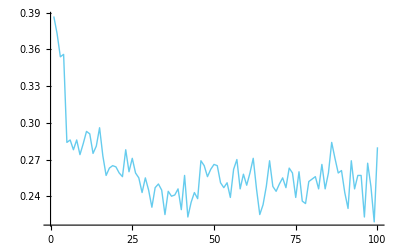

```mathematica
ListPlot[scores,Joined->True,PlotRange->All]
```

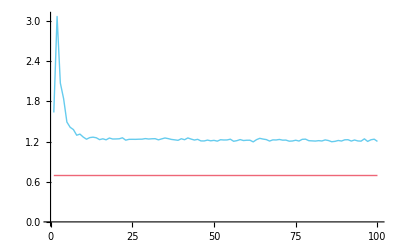

```mathematica
ListPlot[{surpr,-Table[Log@0.5,{nsamples}]},GridLines->None,Joined->True,PlotRange->All]
```

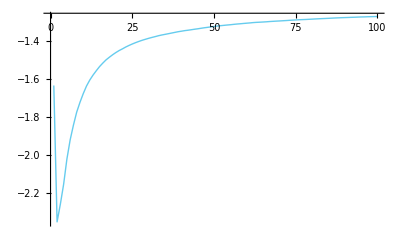

```mathematica
ListPlot[lev/Range@Length@lev,Joined->True,PlotRange->All]
```

```mathematica
(* define a parametric family for a 3-outcome space *)
```

```mathematica
expsum[t_]=Table[(1+KroneckerDelta[s,1])*Exp[t*s],{s,{0,2,1}}];
z[t_]=Total@expsum[t];
prob[t_]=Simplify[expsum[t]/z[t]]
```

{1/((1+ⅇ^t)^2),ⅇ^(2 t)/((1+ⅇ^t)^2),(2 ⅇ^t)/((1+ⅇ^t)^2)}

```mathematica
(* coords transfs to plot the two-distribution space *)
```

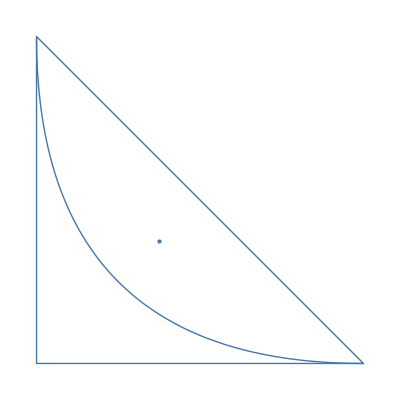

```mathematica
offset=9/8;
c1[p_]:=p[[{1,2}]];

plotfreqs[freqs_]:=Block[{nfreqs=(#/Total@#)&@Flatten@freqs},Graphics[{{PointSize@Large,purpleblue,Point[c1@nfreqs]}}]];
plotcfreqs[freqs_]:=Block[{nfreqs=(#/Total@#)&@Flatten@freqs},Graphics[{{Thick,purpleblue,Circle[c1@nfreqs,0.02]}}]];
sp1={purpleblue,Thin,Line[{{0,0},{1,0},{0,1},{0,0}}]};

pplot1=ParametricPlot[c1@prob[t],{t,-100,100},Axes->None,PlotRange->All,AspectRatio->Auto,PlotStyle->{Thick,purpleblue}];

doms={Graphics[{sp1}],pplot1};
Show[{doms,plotfreqs[ofreqs]},PlotRange->All]
```

```mathematica
{lh1[[nsamples]],lh2[[nsamples]]}
```

{{0.252496,0.252496,0.495009},{0.256039,0.258316,0.485645}}

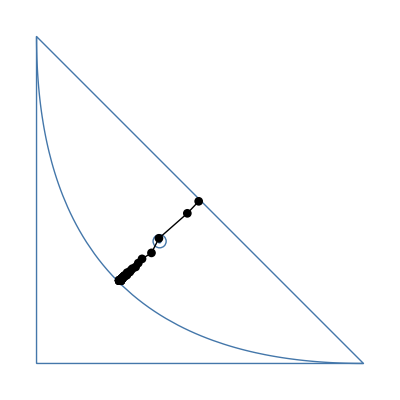

```mathematica
subrange=Round[Range[1,nsamples,nsamples/nsamples]];rplot1=ListPlot[Table[c1@pro[[i]],{i,subrange}],Axes->None,PlotRange->All,PlotStyle->Black,Joined->True,PlotMarkers->Auto];
Show[{doms,plotfreqs@ofreqs,plotcfreqs@ffreqs,rplot1},PlotRange->All]
```

```mathematica
(* algorithm to predict & update from data *)
```

```mathematica
expsum[t_]=Table[(1+KroneckerDelta[s,1])*Exp[t*s],{s,{0,2,1}}];
z[t_]=Total@expsum[t];
prob[t_]=Simplify[expsum[t]/z[t]]
```

{1/((1+ⅇ^t)^2),ⅇ^(2 t)/((1+ⅇ^t)^2),(2 ⅇ^t)/((1+ⅇ^t)^2)}

```mathematica
prob[0]//N
```

{0.25,0.25,0.5}

```mathematica
NIntegrate[prob[t]*prior[t,0,1.686834785358595],{t,-Infinity,Infinity}]
```

{0.333333,0.333333,0.333333}

```mathematica
f[s_]:=NIntegrate[prob[t]*prior[t,0,s],{t,-Infinity,Infinity}][[3]]
```

```mathematica
NMinimize[(1/3-f[ss])^2,ss]
```

{1.70334×10^-18,{ss→1.68683}}

```mathematica
NumberForm[1.686834785358595,102]
```

1.686834785358595

```mathematica
prior[t_,m_,s_]:=PDF[NormalDistribution[m,s],t];
```

```mathematica
(* generate data *)
```

```mathematica
rfreqs=Flatten@{{{1/2,1/2}*10/10,0/10}};
samples=100;
data=RandomChoice[rfreqs->Range[3],samples];
```

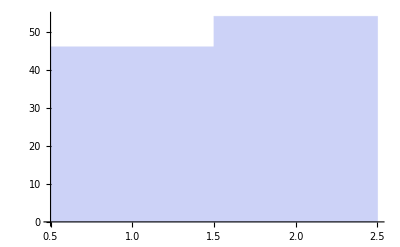

```mathematica
Histogram[data]
```

```mathematica
ProgressIndicator[Dynamic[i],{0,samples}]
```

```mathematica
samples=Length[data];m=0;s=10;freqs=Table[0,{3}];evidence=1;
probh=Table[Null,{samples}];
surph=Table[Null,{samples}];
logev=Table[Null,{samples}];

Do[
integral=
NIntegrate[prob[t]*Times@@(prob[t]^freqs)*prior[t,m,s],{t,-Infinity,+Infinity}];
(*Print[{i,integral//MF}];*)
probh[[i]]=integral/evidence;
surph[[i]]=-Log[probh[[i,data[[i]]]]];

evidence=integral[[data[[i]]]];
logev[[i]]=Log[evidence];
++freqs[[data[[i]]]];
,{i,samples}]
```

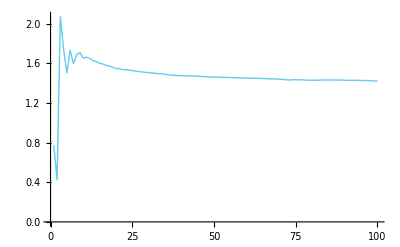

```mathematica
ListPlot[-logev/Range[samples],Joined->True,PlotRange->All]
```

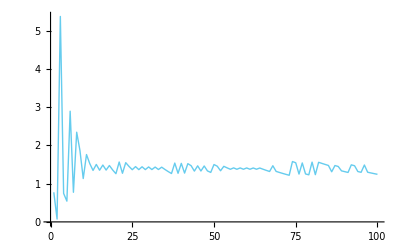

```mathematica
ListPlot[surph,Joined->True,PlotRange->All]
```

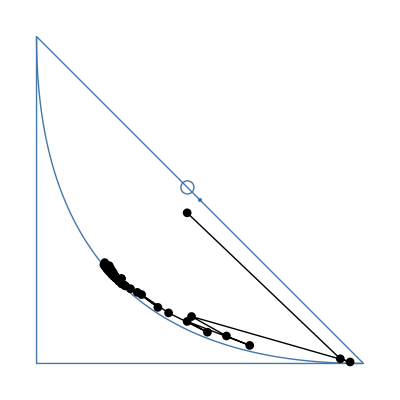

```mathematica
subrange=Round[Range[1,samples,samples/samples]];ppplot1=ParametricPlot[c1@prob[t],{t,-100,100},Axes->None,PlotRange->All,AspectRatio->Auto,PlotStyle->{Thick,purpleblue}];

ddoms={Graphics[{sp1}],ppplot1};rplot1=ListPlot[Table[c1@probh[[i]],{i,subrange}],Axes->None,PlotRange->All,PlotStyle->Black,Joined->True,PlotMarkers->Auto];
Show[{ddoms,plotfreqs@rfreqs,plotcfreqs@freqs,rplot1},PlotRange->All]
```

```mathematica
nobs=15;data=RandomChoice[freq->{1,2,3},nobs];
```

```mathematica
nsamples=25;
updens[0]=FS[(m-1)^4/Integrate[(m-1)^4,{m,0,2}]];
upprob[0]=FS@NIntegrate[probm*updens[0],{m,0,2}];
```

```mathematica
Do[
datas=RandomSample[data];
updens[sample,0]=updens[0];
upprob[sample,0]=upprob[0];
Do[Print[sample," -",i];updens[sample,i]=Assuming[0<m<2,FS[probm[[datas[[i]]]]*updens[sample,i-1]/NIntegrate[probm[[datas[[i]]]]*updens[sample,i-1],{m,0,2}]]];
upprob[sample,i]=FS@NIntegrate[probm*updens[sample,i],{m,0,2}],{i,1,nobs}];,{sample,1,nsamples}];
```

```mathematica
Do[upprob[i]=Mean[Table[upprob[sample,i],{sample,nsamples}]],{i,nobs}];{upprob[nobs],freq}//N//MF
```

(0.107483 | 0.252758 | 0.639759
0.2 | 0.2 | 0.6)

```mathematica
Table[upprob[samples,nobs],{samples,8}]//MF
```

(0.107483 | 0.252758 | 0.639759
0.107483 | 0.252758 | 0.639759
0.107483 | 0.252758 | 0.639759
0.107483 | 0.252758 | 0.639759
0.107483 | 0.252758 | 0.639759
0.107483 | 0.252758 | 0.639759
0.107483 | 0.252758 | 0.639759
0.107483 | 0.252758 | 0.639759)

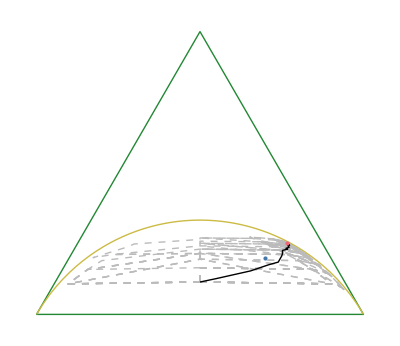

```mathematica
Show[Join[{triangle,parplot,Graphics[{purpleblue,PointSize[Medium],Point[finpoints.freq]}]},
Table[Graphics[{Dashed,Thin,grey,Line[T[finpoints.T[Table[upprob[sample,i],{i,0,nobs}]]]]}],{sample,nsamples}],{
Graphics@Line[T[finpoints.T[Table[upprob[i],{i,0,nobs}]]]],Graphics[{red,PointSize[Medium],Point[finpoints.upprob[nobs]]}]}]]
```

```mathematica
expdf0["overlearning1"]
```

overlearning1.pdf

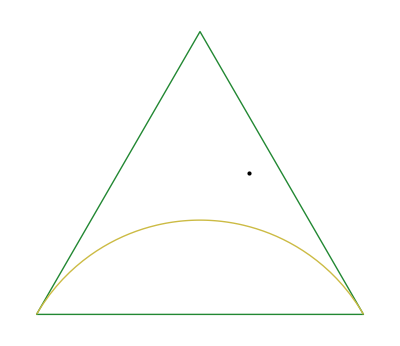

```mathematica
freq2={1/10,1-5/10,4/10};Show[{triangle,parplot,Graphics@Point[finpoints.freq2]}]
```

```mathematica
nobs2=15;data2=RandomChoice[freq2->{1,2,3},nobs2];
```

```mathematica
nsamples2=25;
updens2[0]=FS[(m-1)^4/Integrate[(m-1)^4,{m,0,2}]];
upprob2[0]=FS@NIntegrate[probm*updens2[0],{m,0,2}];
```

```mathematica
Do[
datas=RandomSample[data2];
updens2[sample,0]=updens2[0];
upprob2[sample,0]=upprob2[0];
Do[Print[sample," -",i];updens2[sample,i]=Assuming[0<m<2,FS[probm[[datas[[i]]]]*updens2[sample,i-1]/NIntegrate[probm[[datas[[i]]]]*updens2[sample,i-1],{m,0,2}]]];
upprob2[sample,i]=FS@NIntegrate[probm*updens2[sample,i],{m,0,2}],{i,1,nobs2}];,{sample,1,nsamples2}];
```

```mathematica
Do[upprob2[i]=Mean[Table[upprob2[sample,i],{sample,nsamples2}]],{i,nobs2}];{upprob2[nobs2],freq2}//N//MF
```

(0.13709 | 0.271276 | 0.591634
0.1 | 0.5 | 0.4)

```mathematica
Table[upprob2[samples,nobs2],{samples,8}]//MF
```

(0.13709 | 0.271276 | 0.591634
0.13709 | 0.271276 | 0.591634
0.13709 | 0.271276 | 0.591634
0.13709 | 0.271276 | 0.591634
0.13709 | 0.271276 | 0.591634
0.13709 | 0.271276 | 0.591634
0.13709 | 0.271276 | 0.591634
0.13709 | 0.271276 | 0.591634)

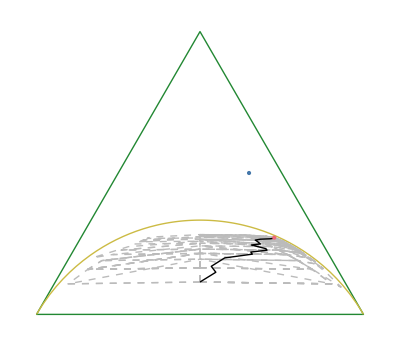

```mathematica
Show[Join[{triangle,parplot,Graphics[{purpleblue,PointSize[Medium],Point[finpoints.freq2]}]},
Table[Graphics[{Dashed,Thin,grey,Line[T[finpoints.T[Table[upprob2[sample,i],{i,0,nobs2}]]]]}],{sample,nsamples2}],{
Graphics@Line[T[finpoints.T[Table[upprob2[i],{i,0,nobs2}]]]],Graphics[{red,PointSize[Medium],Point[finpoints.upprob2[nobs2]]}]}]]
```

```mathematica
expdf0["overlearning2"]
```

overlearning2.pdf